## Setup

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/sawin/quenching_integration/mathematica

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,ListLogPlot,LogLinearPlot,Histogram,DensityHistogram,ListStepPlot},Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

```mathematica
myLog[x_]:={x[[1]],x[[2]],Log[x[[3]]]}
```

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
```

```mathematica
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/usr/bin/xelatex","Ghostscript"->"/usr/bin/gs"];
myMaTeX[x_]:= MaTeX[x,"Preamble"->{"\\usepackage{fontspec}","\\setmainfont{DejaVu Serif}"},FontSize->16]
```

```mathematica
myMaTeX2[x_]:= MaTeX[x,FontSize->18]
```

## Load params

```mathematica
myParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../input/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&]
myDict=Association[Table[myParams[[i,1]]->ToExpression[myParams[[i,2]]],{i,1,Length[myParams]}]];
```

{{collisionType,0},{particleType,0},{upsilonState,0},{alphas,0},{lambdaQCD,0.308},{qhat0,0.075},{lp,1.5},{lA,11.41},{lB,11.41},{massp,0.938},{rootsnn,5023},{Ny,21},{Npt,81},{y_min,-5.0},{y_max,5.0},{ptmin,0.1},{ptmax,40.1}}

```mathematica
roots = myDict["rootsnn"]
```

5023

```mathematica
M =If[myDict["particleType"]==1 ,3.43,9.95] (*particleType = 0 => Upsilon, 1 => J/Psi*)
```

9.95

```mathematica
cE = Which[roots==5023,"5.02",roots==8160,"8.16"]
```

5.02

```mathematica
Leff=myDict["lA"]
```

11.41

```mathematica
coupling=If[myDict["alphas"]==0,"RunningCoupling","Constant"]
```

RunningCoupling

## General functions

```mathematica
Mperp2[pt_] = pt^2+M^2; (* GeV ^2 *)
Mperp[pt_] = Sqrt[Mperp2[pt]]; (* GeV *)
ymaxFunction[pt_] = Log[roots/Mperp[pt]];
ptmaxFunction[y_]=Sqrt[(roots Exp[-y])^2 - M^2];
```

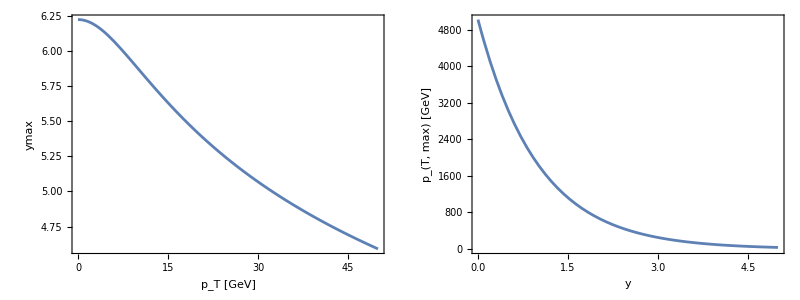

```mathematica
Grid[{{Plot[ymaxFunction[pt],{pt,0,50},FrameLabel->{"p_T [GeV]","ymax"}],Plot[ptmaxFunction[y],{y,0,5},FrameLabel->{"y","p_(T, max) [GeV]"}]}}]
```

## Read pA data

```mathematica
pAresultLog=Interpolation[myLog/@Import[wd<>"/../output/pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pAerrorLog=Interpolation[myLog/@Import[wd<>"/../output/pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pAresultLog[[1,1]]
{ptmin,ptmax} = pAresultLog[[1,2]]
pAresult[y_,pt_]:=Exp[pAresultLog[y,pt]]
pAerror[y_,pt_]:=Exp[pAerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
Plot3D[pAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[pAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

## Read AB data

```mathematica
ABresultLog=Interpolation[myLog/@Import[wd<>"/../output/AB-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
ABerrorLog=Interpolation[myLog/@Import[wd<>"/../output/AB-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = ABresultLog[[1,1]]
{ptmin,ptmax} = ABresultLog[[1,2]]
ABresult[y_,pt_]:=Exp[ABresultLog[y,pt]]
ABerror[y_,pt_]:=Exp[ABerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
Plot3D[ABresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[ABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

## Read pp data

```mathematica
ppresultLog=Interpolation[myLog/@Import[wd<>"/../output/pp-cross-section.tsv"],InterpolationOrder->Automatic];
ppresult[y_,pt_]:=Exp[ppresultLog[y,pt]]
```

```mathematica
Plot3D[ppresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

## Read RAB data

```mathematica
RABresult=Interpolation[Import[wd<>"/../output/RAB.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RABerror=Interpolation[Import[wd<>"/../output/RAB.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} = RABresult[[1,1]];
{ptmin,ptmax} =RABresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RABresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RABerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RABresultU[y_,pt_]=RABresult[y,pt]+RABerror[y,pt];
RABresultL[y_,pt_]=RABresult[y,pt]-RABerror[y,pt];
```

```mathematica
myPlotY[pt_]:=Plot[{RABresult[y,pt],RABresultL[y,pt],RABresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_AB"},ImageSize->400,PlotRange->Automatic]
myPlotPT[y_]:=Plot[{RABresult[y,pt],RABresultL[y,pt],RABresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_AB"},ImageSize->400,PlotRange->Automatic]
```

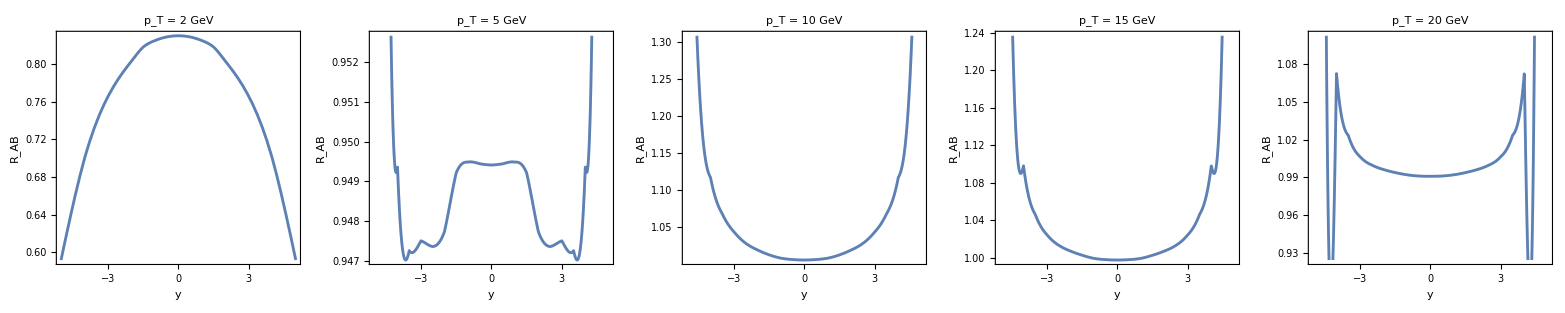

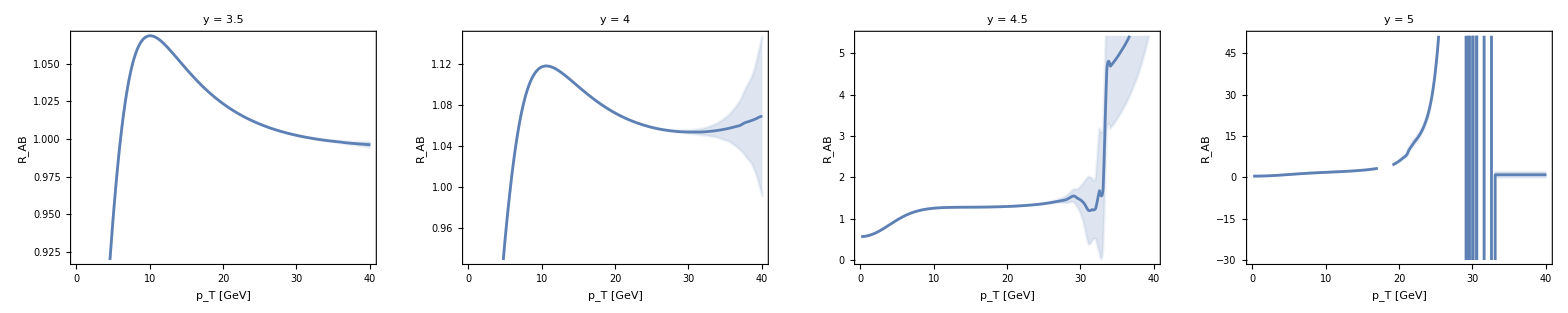

```mathematica
p1=Grid[{{myPlotY[2],myPlotY[5],myPlotY[10],myPlotY[15],myPlotY[20]}}]
p2=Grid[{{myPlotPT[3.5],myPlotPT[4],myPlotPT[4.5],myPlotPT[5]}}]
```

```mathematica
Export[wd<>"/figures/RAA_vs_y_Leff"<>ToString[Leff]<>"_"<>coupling<>".pdf",p1]
Export[wd<>"/figures/RAA_vs_pT_Leff"<>ToString[Leff]<>"_"<>coupling<>".pdf",p2]
```

/home/sawin/quenching_integration/mathematica/figures/RAA_vs_y_Leff11.41_RunningCoupling.pdf

/home/sawin/quenching_integration/mathematica/figures/RAA_vs_pT_Leff11.41_RunningCoupling.pdf

## Read RpA data

```mathematica
RpAresult=Interpolation[Import[wd<>"/../output/RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpAerror=Interpolation[Import[wd<>"/../output/RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpAresult[[1,1]];
{ptmin,ptmax} =RpAresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Plot3D[RpAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpAresultU[y_,pt_]=RpAresult[y,pt]+RpAerror[y,pt];
RpAresultL[y_,pt_]=RpAresult[y,pt]-RpAerror[y,pt];
```

```mathematica
mypAPlotY[pt_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,1.5}]
mypAPlotPT[y_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,1.5}]
```

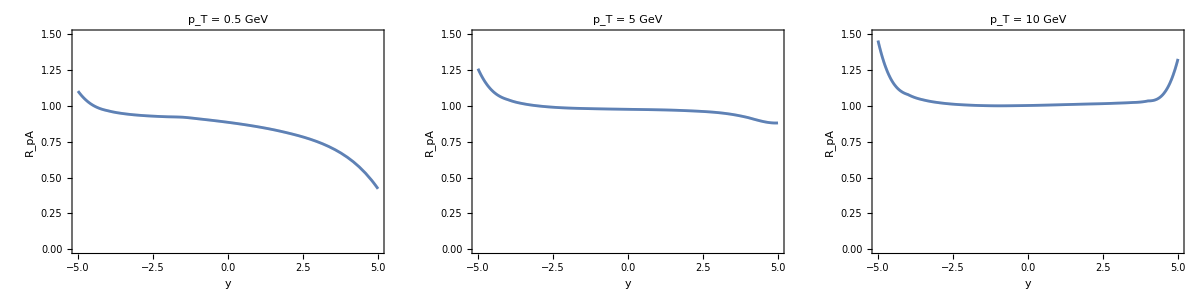

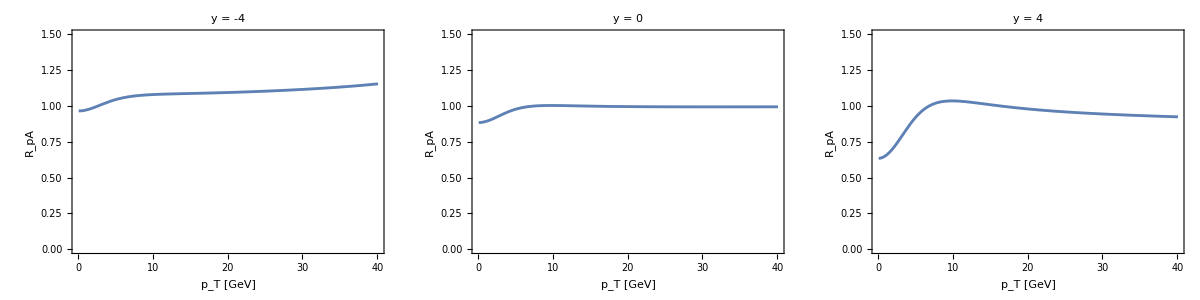

```mathematica
p3=Grid[{{mypAPlotY[0.5],mypAPlotY[5],mypAPlotY[10]}}]
p4=Grid[{{mypAPlotPT[-4],mypAPlotPT[0],mypAPlotPT[4]}}]
```

```mathematica
Export[wd<>"/figures/RpA_vs_y_Leff"<>ToString[Leff]<>"_"<>coupling<>".pdf",p3]
Export[wd<>"/figures/RpA_vs_pT_Leff"<>ToString[Leff]<>"_"<>coupling<>".pdf",p4]
```

/home/sawin/quenching_integration/mathematica/figures/RpA_vs_y_Leff11.41_RunningCoupling.pdf

/home/sawin/quenching_integration/mathematica/figures/RpA_vs_pT_Leff11.41_RunningCoupling.pdf

## RAB vs y & pT binned Plots

### Rapidity Dependent (p_T averaged)

```mathematica
ptmin = 0.1;
ptmax = 20;
```

```mathematica
RpAresultPTavg[{ymin_,ymax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[RABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ybins = -5 + 0.5Range[0,20]
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
binnedRPAelossVSY = RpAresultPTavg/@ Transpose[{Drop[ybins,-1],Drop[ybins,1]}];
```

NIntegrate::inumr: The integrand ⅇ^(InterpolatingFunction[{{-5.,5.},{0.1,40.1}},{5,3,0,{21,81},{4,4},0,0,0,0,Automatic,{},{},False},{{-5.,-4.5,«17»,4.5,5.},{«1»}},{«1»},{Automatic,Automatic}][0,«2»]) pt «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{17.1,17.6},{-5.,-4.5}}.

NIntegrate::inumr: The integrand ⅇ^(InterpolatingFunction[{{-5.,5.},{0.1,40.1}},{5,3,0,{21,81},{4,4},0,0,0,0,Automatic,{},{},False},{{-5.,-4.5,«17»,4.5,5.},{«1»}},{«1»},{Automatic,Automatic}][0,«2»]) pt «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{17.1,17.6},{-4.5,-4.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
binnedRPAElossDataVSY = Transpose[{Drop[ybins,-1],binnedRPAelossVSY}]
```

NIntegrate::inumr: The integrand ⅇ^(InterpolatingFunction[{{-5.,5.},{0.1,40.1}},{5,3,0,{21,81},{4,4},0,0,0,0,Automatic,{},{},False},{{-5.,-4.5,«17»,4.5,5.},{«1»}},{«1»},{Automatic,Automatic}][0,«2»]) pt «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{17.1,17.6},{-5.,-4.5}}.

NIntegrate::inumr: The integrand ⅇ^(InterpolatingFunction[{{-5.,5.},{0.1,40.1}},{5,3,0,{21,81},{4,4},0,0,0,0,Automatic,{},{},False},{{-5.,-4.5,«17»,4.5,5.},{«1»}},{«1»},{Automatic,Automatic}][0,«2»]) pt «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{17.1,17.6},{-4.5,-4.}}.

NIntegrate::inumr: The integrand ⅇ^(InterpolatingFunction[{{-5.,5.},{0.1,40.1}},{5,3,0,{21,81},{4,4},0,0,0,0,Automatic,{},{},False},{{-5.,-4.5,«17»,4.5,5.},{«1»}},{«1»},{Automatic,Automatic}][0,«2»]) pt «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{17.1,17.6},{4.,4.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{-5.,0.0101045 NIntegrate[RABresult[y,pt] ABresult[0,pt] pt,{pt,ptmin,ptmax},{y,-5.,-4.5}]},{-4.5,0.0101045 NIntegrate[RABresult[y,pt] ABresult[0,pt] pt,{pt,ptmin,ptmax},{y,-4.5,-4.}]},{-4.,0.047271},{-3.5,0.047374},{-3.,0.0475333},{-2.5,0.0476903},{-2.,0.0478804},{-1.5,0.0480137},{-1.,0.0480603},{-0.5,0.048086},{0.,0.048086},{0.5,0.0480603},{1.,0.0480137},{1.5,0.0478804},{2.,0.0476903},{2.5,0.0475333},{3.,0.047374},{3.5,0.047271},{4.,0.0101045 NIntegrate[RABresult[y,pt] ABresult[0,pt] pt,{pt,ptmin,ptmax},{y,4.,4.5}]},{4.5,0.0101045 NIntegrate[RABresult[y,pt] ABresult[0,pt] pt,{pt,ptmin,ptmax},{y,4.5,5.}]}}

```mathematica
rapidityplot=ListStepPlot[binnedRPAElossDataVSY,Right,PlotRange->{{-5,5},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ptmin]<>"<$p_T$<"<>ToString[ptmax]<>" GeV }"],{1.5,0.05}]},FrameLabel->{"y","R_AA"}]
```

NIntegrate::inumr: The integrand ⅇ^(InterpolatingFunction[{{-5.,5.},{0.1,40.1}},{5,3,0,{21,81},{4,4},0,0,0,0,Automatic,{},{},False},{{-5.,-4.5,«17»,4.5,5.},{«1»}},{«1»},{Automatic,Automatic}][0,«2»]) pt «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{17.1,17.6},{-5.,-4.5}}.

NIntegrate::inumr: The integrand ⅇ^(InterpolatingFunction[{{-5.,5.},{0.1,40.1}},{5,3,0,{21,81},{4,4},0,0,0,0,Automatic,{},{},False},{{-5.,-4.5,«17»,4.5,5.},{«1»}},{«1»},{Automatic,Automatic}][0,«2»]) pt «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{17.1,17.6},{-4.5,-4.}}.

NIntegrate::inumr: The integrand ⅇ^(InterpolatingFunction[{{-5.,5.},{0.1,40.1}},{5,3,0,{21,81},{4,4},0,0,0,0,Automatic,{},{},False},{{-5.,-4.5,«17»,4.5,5.},{«1»}},{«1»},{Automatic,Automatic}][0,«2»]) pt «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{17.1,17.6},{4.,4.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

### p_T Dependent: Forward(1 = 1.5 < y < 4, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{1.5,4},Length[myPTBins]]
```

{{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

4

1.5

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{1.5,4,0.,2.5},{1.5,4,2.5,5.},{1.5,4,5.,7.5},{1.5,4,7.5,10.},{1.5,4,10.,12.5},{1.5,4,12.5,15.},{1.5,4,15.,17.5},{1.5,4,17.5,20.},{1.5,4,20.,22.5},{1.5,4,22.5,25.},{1.5,4,25.,27.5},{1.5,4,27.5,30.},{1.5,4,30.,32.5},{1.5,4,32.5,35.},{1.5,4,35.,37.5},{1.5,4,37.5,40.},{1.5,4,40.,42.5},{1.5,4,42.5,45.},{1.5,4,45.,47.5},{1.5,4,47.5,50.}}

```mathematica
binnedRPAelossVSPT1 =RpAresultAvg/@myBins1
```

{0.658475,0.765782,0.876495,0.929162,0.943184,0.944129,0.942489,0.941169,0.94065,0.940769,0.941215,0.941871,0.94342,0.945172,0.94617,0.94601,0.93951,0.910321,0.83764,0.700595}

```mathematica
binnedRPAelossDataVSPT1  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT1}]
```

{{0.,0.658475},{2.5,0.765782},{5.,0.876495},{7.5,0.929162},{10.,0.943184},{12.5,0.944129},{15.,0.942489},{17.5,0.941169},{20.,0.94065},{22.5,0.940769},{25.,0.941215},{27.5,0.941871},{30.,0.94342},{32.5,0.945172},{35.,0.94617},{37.5,0.94601},{40.,0.93951},{42.5,0.910321},{45.,0.83764},{47.5,0.700595}}

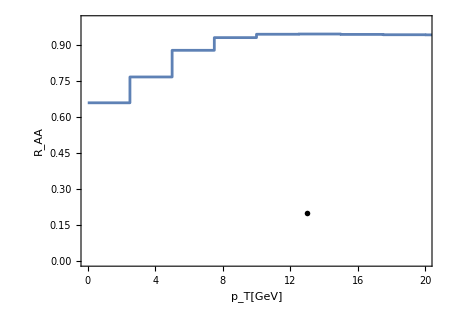

```mathematica
forwardplot= ListStepPlot[binnedRPAelossDataVSPT1,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T[GeV]","R_AA"}]
```

### p_T Dependent: Backward(2 = -5 < y < -2.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-5,2.5},Length[myPTBins]]
```

{{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-5,2.5,0.,2.5},{-5,2.5,2.5,5.},{-5,2.5,5.,7.5},{-5,2.5,7.5,10.},{-5,2.5,10.,12.5},{-5,2.5,12.5,15.},{-5,2.5,15.,17.5},{-5,2.5,17.5,20.},{-5,2.5,20.,22.5},{-5,2.5,22.5,25.},{-5,2.5,25.,27.5},{-5,2.5,27.5,30.},{-5,2.5,30.,32.5},{-5,2.5,32.5,35.},{-5,2.5,35.,37.5},{-5,2.5,37.5,40.},{-5,2.5,40.,42.5},{-5,2.5,42.5,45.},{-5,2.5,45.,47.5},{-5,2.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

2.5

-5

```mathematica
binnedRPAelossVSPT2 =RpAresultAvg/@myBins1
```

{0.671633,0.773904,0.883208,0.941445,0.964703,0.97822,0.997774,1.00426,0.970082,1.18808,18.8125,-134917.,3.7899×10^17,-9.36024×10^15,1.02481,1.06071,1.16732,1.47916,2.1547,3.35264}

```mathematica
binnedRPAelossDataVSPT2  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT2}]
```

{{0.,0.671633},{2.5,0.773904},{5.,0.883208},{7.5,0.941445},{10.,0.964703},{12.5,0.97822},{15.,0.997774},{17.5,1.00426},{20.,0.970082},{22.5,1.18808},{25.,18.8125},{27.5,-134917.},{30.,3.7899×10^17},{32.5,-9.36024×10^15},{35.,1.02481},{37.5,1.06071},{40.,1.16732},{42.5,1.47916},{45.,2.1547},{47.5,3.35264}}

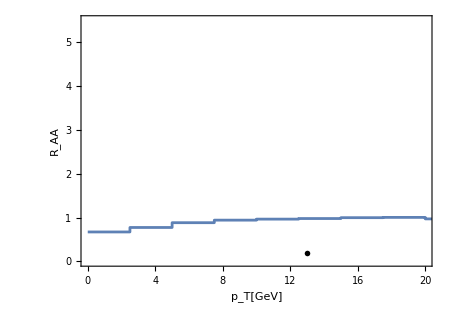

```mathematica
backwardplot=ListStepPlot[binnedRPAelossDataVSPT2,Right,PlotRange->{{0,20},{0,5.5}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T[GeV]","R_AA"}]
```

### p_T Dependent: Mid(3 = -1.93 < y < -1.93, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-1.93,1.93},Length[myPTBins]]
```

{{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-1.93,1.93,0.,2.5},{-1.93,1.93,2.5,5.},{-1.93,1.93,5.,7.5},{-1.93,1.93,7.5,10.},{-1.93,1.93,10.,12.5},{-1.93,1.93,12.5,15.},{-1.93,1.93,15.,17.5},{-1.93,1.93,17.5,20.},{-1.93,1.93,20.,22.5},{-1.93,1.93,22.5,25.},{-1.93,1.93,25.,27.5},{-1.93,1.93,27.5,30.},{-1.93,1.93,30.,32.5},{-1.93,1.93,32.5,35.},{-1.93,1.93,35.,37.5},{-1.93,1.93,37.5,40.},{-1.93,1.93,40.,42.5},{-1.93,1.93,42.5,45.},{-1.93,1.93,45.,47.5},{-1.93,1.93,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.93

-1.93

```mathematica
binnedRPAelossVSPT3 =RpAresultAvg/@myBins1
```

{0.730895,0.813183,0.892453,0.928588,0.939447,0.942455,0.943983,0.945607,0.947535,0.949665,0.951871,0.954041,0.95614,0.958142,0.960034,0.961808,0.963418,0.964398,0.964046,0.961648}

```mathematica
binnedRPAelossDataVSPT3  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT3}]
```

{{0.,0.730895},{2.5,0.813183},{5.,0.892453},{7.5,0.928588},{10.,0.939447},{12.5,0.942455},{15.,0.943983},{17.5,0.945607},{20.,0.947535},{22.5,0.949665},{25.,0.951871},{27.5,0.954041},{30.,0.95614},{32.5,0.958142},{35.,0.960034},{37.5,0.961808},{40.,0.963418},{42.5,0.964398},{45.,0.964046},{47.5,0.961648}}

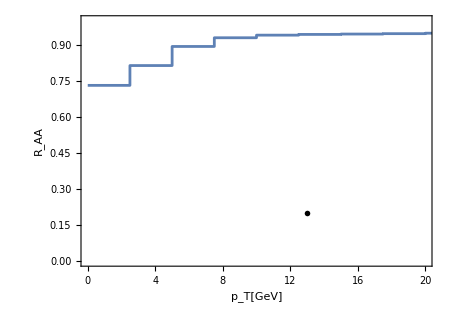

```mathematica
centralplot=ListStepPlot[binnedRPAelossDataVSPT3,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T[GeV]","R_AA"}]
```

### p_T Dependent: Back(4 = -2 < y < -1.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RABresult[y,pt]*ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[ABresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-2,1.5},Length[myPTBins]]
```

{{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-2,1.5,0.,2.5},{-2,1.5,2.5,5.},{-2,1.5,5.,7.5},{-2,1.5,7.5,10.},{-2,1.5,10.,12.5},{-2,1.5,12.5,15.},{-2,1.5,15.,17.5},{-2,1.5,17.5,20.},{-2,1.5,20.,22.5},{-2,1.5,22.5,25.},{-2,1.5,25.,27.5},{-2,1.5,27.5,30.},{-2,1.5,30.,32.5},{-2,1.5,32.5,35.},{-2,1.5,35.,37.5},{-2,1.5,37.5,40.},{-2,1.5,40.,42.5},{-2,1.5,42.5,45.},{-2,1.5,45.,47.5},{-2,1.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.5

-2

```mathematica
binnedRPAelossVSPT4 =RpAresultAvg/@myBins1
```

{0.732101,0.813882,0.89261,0.928499,0.939341,0.942415,0.944021,0.945712,0.947692,0.949861,0.952095,0.954283,0.956393,0.958402,0.960298,0.962073,0.96368,0.964632,0.964197,0.961638}

```mathematica
binnedRPAelossDataVSPT4  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT4}]
```

{{0.,0.732101},{2.5,0.813882},{5.,0.89261},{7.5,0.928499},{10.,0.939341},{12.5,0.942415},{15.,0.944021},{17.5,0.945712},{20.,0.947692},{22.5,0.949861},{25.,0.952095},{27.5,0.954283},{30.,0.956393},{32.5,0.958402},{35.,0.960298},{37.5,0.962073},{40.,0.96368},{42.5,0.964632},{45.,0.964197},{47.5,0.961638}}

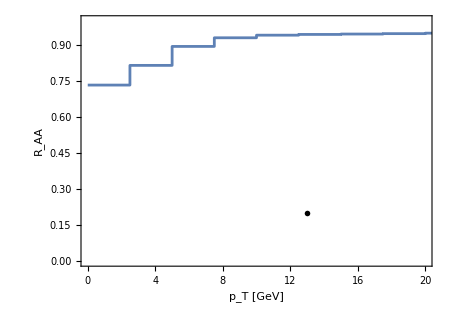

```mathematica
backplot=ListStepPlot[binnedRPAelossDataVSPT4,Right,PlotRange->{{0,20},{0,1.0}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T [GeV]","R_AA"}]
```

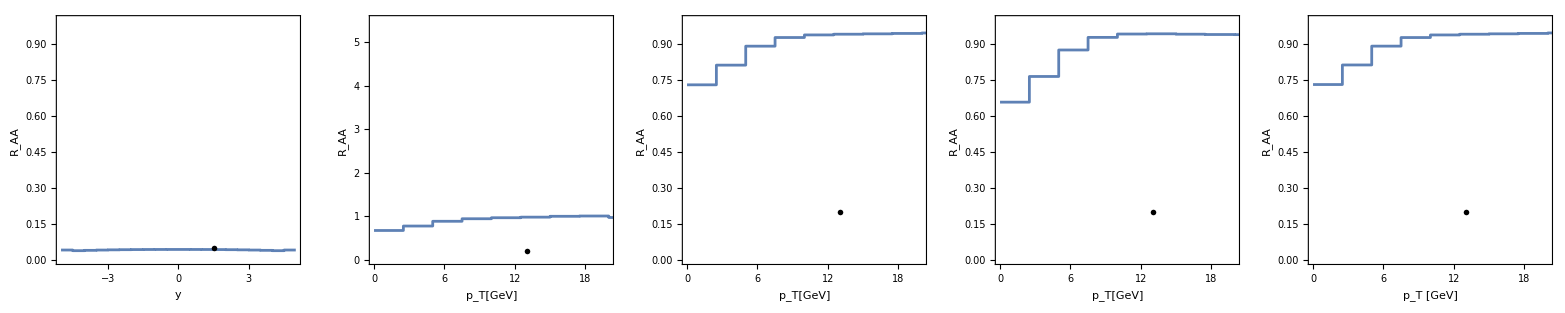

```mathematica
AAplt=Grid[{{rapidityplot,backwardplot,centralplot,forwardplot,backplot}}]
```

```mathematica
Export[wd<>"/figures/RAA_vs_YpT_Binned_Leff"<>ToString[Leff]<>"_RunningCoupling.pdf",AAplt]
```

/home/sawin/quenching_integration/mathematica/figures/RAA_vs_YpT_Binned_Leff11.41_RunningCoupling.pdf

## RpA vs y & pT binned Plots

### Rapidity Dependent (p_T averaged)

```mathematica
ptmin = 0.1;
ptmax = 20;
```

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultPTavg[{ymin_,ymax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ybins = -5 + 0.5Range[0,20]
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
binnedRPAelossVSY = RpAresultPTavg/@ Transpose[{Drop[ybins,-1],Drop[ybins,1]}];
```

```mathematica
binnedRPAElossDataVSY = Transpose[{Drop[ybins,-1],binnedRPAelossVSY}]
```

{{-5.,1.17555},{-4.5,1.05627},{-4.,1.01747},{-3.5,0.996922},{-3.,0.985101},{-2.5,0.977915},{-2.,0.973761},{-1.5,0.970145},{-1.,0.966138},{-0.5,0.962501},{0.,0.958727},{0.5,0.954523},{1.,0.949496},{1.5,0.942997},{2.,0.934741},{2.5,0.924144},{3.,0.90904},{3.5,0.887091},{4.,0.858107},{4.5,0.853197}}

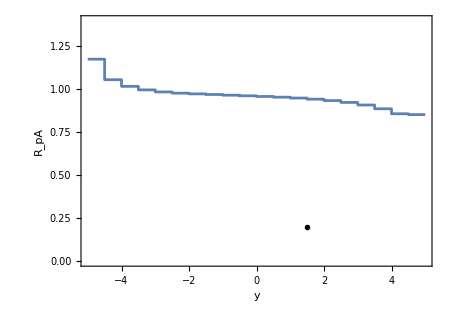

```mathematica
rapidityplot=ListStepPlot[binnedRPAElossDataVSY,Right,PlotRange->{{-5,5},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ptmin]<>"<$p_T$<"<>ToString[ptmax]<>" GeV }"],{1.5,0.2}]},FrameLabel->{"y","R_pA"}]
```

```mathematica
RpAresultPTavg[{-5,5}]
```

0.962692

### p_T Dependent: Forward(1 = 1.5 < y < 4, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{1.5,4},Length[myPTBins]]
```

{{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

4

1.5

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{1.5,4,0.,2.5},{1.5,4,2.5,5.},{1.5,4,5.,7.5},{1.5,4,7.5,10.},{1.5,4,10.,12.5},{1.5,4,12.5,15.},{1.5,4,15.,17.5},{1.5,4,17.5,20.},{1.5,4,20.,22.5},{1.5,4,22.5,25.},{1.5,4,25.,27.5},{1.5,4,27.5,30.},{1.5,4,30.,32.5},{1.5,4,32.5,35.},{1.5,4,35.,37.5},{1.5,4,37.5,40.},{1.5,4,40.,42.5},{1.5,4,42.5,45.},{1.5,4,45.,47.5},{1.5,4,47.5,50.}}

```mathematica
binnedRPAelossVSPT1 =RpAresultAvg/@myBins1
```

{0.792369,0.893964,0.984761,1.01647,1.01595,1.00672,0.99716,0.989249,0.983076,0.978332,0.974666,0.971738,0.969321,0.967197,0.964987,0.962731,0.960461,0.957619,0.953914,0.949055}

```mathematica
binnedRPAelossDataVSPT1  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT1}]
```

{{0.,0.792369},{2.5,0.893964},{5.,0.984761},{7.5,1.01647},{10.,1.01595},{12.5,1.00672},{15.,0.99716},{17.5,0.989249},{20.,0.983076},{22.5,0.978332},{25.,0.974666},{27.5,0.971738},{30.,0.969321},{32.5,0.967197},{35.,0.964987},{37.5,0.962731},{40.,0.960461},{42.5,0.957619},{45.,0.953914},{47.5,0.949055}}

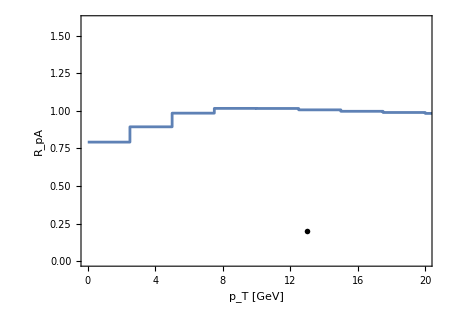

```mathematica
forwardplot= ListStepPlot[binnedRPAelossDataVSPT1,Right,PlotRange->{{0,20},{0,1.6}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T [GeV]","R_pA"}]
```

### p_T Dependent: Backward(2 = -5 < y < -2.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-5,2.5},Length[myPTBins]]
```

{{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-5,2.5,0.,2.5},{-5,2.5,2.5,5.},{-5,2.5,5.,7.5},{-5,2.5,7.5,10.},{-5,2.5,10.,12.5},{-5,2.5,12.5,15.},{-5,2.5,15.,17.5},{-5,2.5,17.5,20.},{-5,2.5,20.,22.5},{-5,2.5,22.5,25.},{-5,2.5,25.,27.5},{-5,2.5,27.5,30.},{-5,2.5,30.,32.5},{-5,2.5,32.5,35.},{-5,2.5,35.,37.5},{-5,2.5,37.5,40.},{-5,2.5,40.,42.5},{-5,2.5,42.5,45.},{-5,2.5,45.,47.5},{-5,2.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

2.5

-5

```mathematica
binnedRPAelossVSPT2 =RpAresultAvg/@myBins1
```

{0.925989,0.97457,1.01658,1.03394,1.0394,1.04299,1.05023,1.07108,1.16607,2.14004,23.7653,-33807.5,3.07183×10^17,-7.59655×10^15,1.1495,1.34123,2.00786,4.01004,8.32064,15.9109}

```mathematica
binnedRPAelossDataVSPT2  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT2}]
```

{{0.,0.925989},{2.5,0.97457},{5.,1.01658},{7.5,1.03394},{10.,1.0394},{12.5,1.04299},{15.,1.05023},{17.5,1.07108},{20.,1.16607},{22.5,2.14004},{25.,23.7653},{27.5,-33807.5},{30.,3.07183×10^17},{32.5,-7.59655×10^15},{35.,1.1495},{37.5,1.34123},{40.,2.00786},{42.5,4.01004},{45.,8.32064},{47.5,15.9109}}

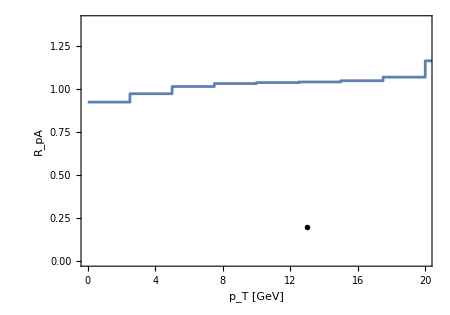

```mathematica
backwardplot=ListStepPlot[binnedRPAelossDataVSPT2,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T [GeV]","R_pA"}]
```

### p_T Dependent: Mid(3 = -1.93 < y < -1.93, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-1.93,1.93},Length[myPTBins]]
```

{{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-1.93,1.93,0.,2.5},{-1.93,1.93,2.5,5.},{-1.93,1.93,5.,7.5},{-1.93,1.93,7.5,10.},{-1.93,1.93,10.,12.5},{-1.93,1.93,12.5,15.},{-1.93,1.93,15.,17.5},{-1.93,1.93,17.5,20.},{-1.93,1.93,20.,22.5},{-1.93,1.93,22.5,25.},{-1.93,1.93,25.,27.5},{-1.93,1.93,27.5,30.},{-1.93,1.93,30.,32.5},{-1.93,1.93,32.5,35.},{-1.93,1.93,35.,37.5},{-1.93,1.93,37.5,40.},{-1.93,1.93,40.,42.5},{-1.93,1.93,42.5,45.},{-1.93,1.93,45.,47.5},{-1.93,1.93,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.93

-1.93

```mathematica
binnedRPAelossVSPT3 =RpAresultAvg/@myBins1
```

{0.899418,0.949109,0.989869,1.00355,1.00417,1.00155,0.998918,0.996927,0.995558,0.994665,0.994111,0.993792,0.993631,0.993577,0.993595,0.993662,0.99377,0.993967,0.994327,0.994923}

```mathematica
binnedRPAelossDataVSPT3  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT3}]
```

{{0.,0.899418},{2.5,0.949109},{5.,0.989869},{7.5,1.00355},{10.,1.00417},{12.5,1.00155},{15.,0.998918},{17.5,0.996927},{20.,0.995558},{22.5,0.994665},{25.,0.994111},{27.5,0.993792},{30.,0.993631},{32.5,0.993577},{35.,0.993595},{37.5,0.993662},{40.,0.99377},{42.5,0.993967},{45.,0.994327},{47.5,0.994923}}

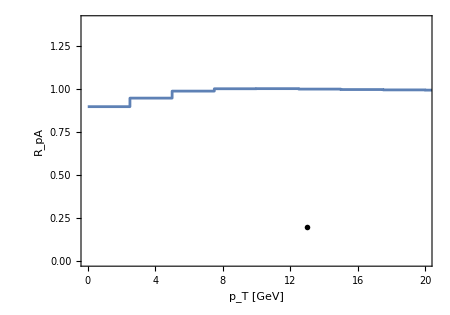

```mathematica
centralplot=ListStepPlot[binnedRPAelossDataVSPT3,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T [GeV]","R_pA"}]
```

### p_T Dependent: Back(4 = -2 < y < -1.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-2,1.5},Length[myPTBins]]
```

{{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-2,1.5,0.,2.5},{-2,1.5,2.5,5.},{-2,1.5,5.,7.5},{-2,1.5,7.5,10.},{-2,1.5,10.,12.5},{-2,1.5,12.5,15.},{-2,1.5,15.,17.5},{-2,1.5,17.5,20.},{-2,1.5,20.,22.5},{-2,1.5,22.5,25.},{-2,1.5,25.,27.5},{-2,1.5,27.5,30.},{-2,1.5,30.,32.5},{-2,1.5,32.5,35.},{-2,1.5,35.,37.5},{-2,1.5,37.5,40.},{-2,1.5,40.,42.5},{-2,1.5,42.5,45.},{-2,1.5,45.,47.5},{-2,1.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.5

-2

```mathematica
binnedRPAelossVSPT4 =RpAresultAvg/@myBins1
```

{0.905983,0.952204,0.989957,1.00271,1.00347,1.00123,0.998961,0.99725,0.996088,0.995346,0.994902,0.994666,0.994565,0.994557,0.99461,0.994704,0.994835,0.99506,0.995465,0.996137}

```mathematica
binnedRPAelossDataVSPT4  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT4}]
```

{{0.,0.905983},{2.5,0.952204},{5.,0.989957},{7.5,1.00271},{10.,1.00347},{12.5,1.00123},{15.,0.998961},{17.5,0.99725},{20.,0.996088},{22.5,0.995346},{25.,0.994902},{27.5,0.994666},{30.,0.994565},{32.5,0.994557},{35.,0.99461},{37.5,0.994704},{40.,0.994835},{42.5,0.99506},{45.,0.995465},{47.5,0.996137}}

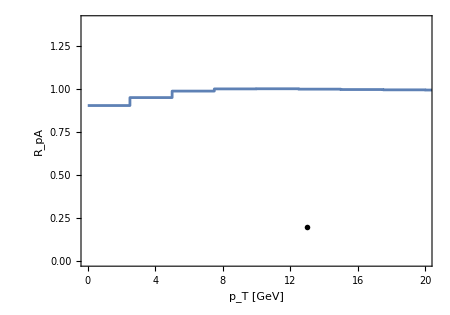

```mathematica
backplot=ListStepPlot[binnedRPAelossDataVSPT4,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T [GeV]","R_pA"}]
```

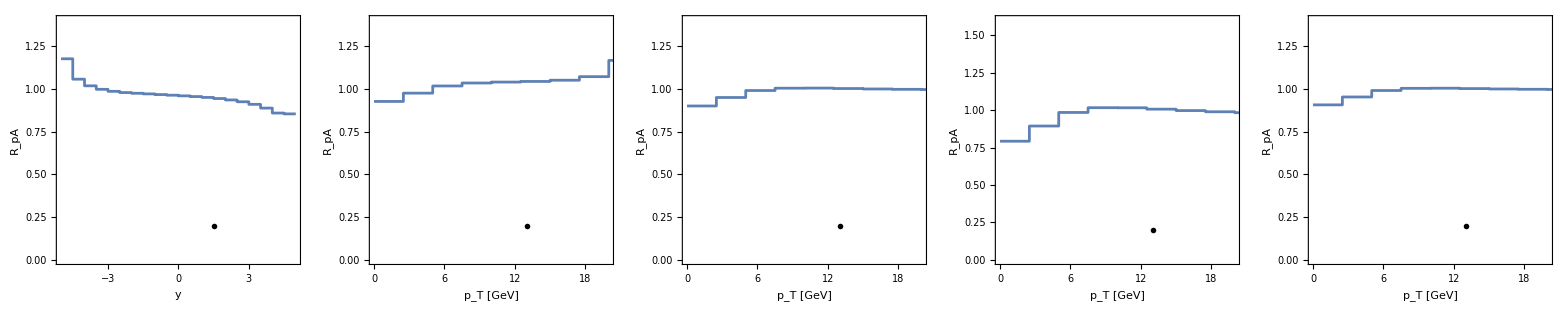

```mathematica
plt=Grid[{{rapidityplot,backwardplot,centralplot,forwardplot,backplot}}]
```

```mathematica
Export[wd<>"/figures/RpA_vs_YpT_Binned_Leff"<>ToString[Leff]<>"_"<>coupling<>".pdf",plt]
```

/home/sawin/quenching_integration/mathematica/figures/RpA_vs_YpT_Binned_Leff11.41_RunningCoupling.pdf